## SI x: Effect of a barrier to gene flow on divergence

In this section, we gather theoretical results on the change in diversity, divergence, and F_st through time, in the presence of barriers to gene flow between two demes, and in one dimensions.  Specifically we give formulae for:
	- the increase in pairwise coalescence times within and between two demes connected by gene flow;
	- the strength of the barrier to gene flow due to two linked loci, between two demes, and across a one-dimensional cline;
	- the effect of a barrier to gene flow in one dimension, compared with a barrier to flow between two demes.

### Change in F_stover time

Suppose that a single well-mixed population, of effective size θN_e splits into two populations, each of size N_e, that exchange migrants symmetrically at rate m. We scale time and migration relative to 2 N_e, so that T=t/(2 N_e), M=2 N_e m.  For two populations, F_st=(T_b-T_w)/(T_b+T_w) is defined in terms of the mean coalescence times for two genes from within a population, or between two populations. These coalescence times are given by (Wakeley, 2008):

∂_T T_w=1+2M(T_b-T_w)-T_w
∂_T T_b=1+2M(T_w-T_b)

Initially, T_w=θ, and T_b=T_w((1+F_0)/(1-F_0)). The terms correspond to the passage of time, migration, and (for T_w only) coalescence. The solution is:

T_w=2+ⅇ^(-1/2 T (1+4 M)) ( (θ-2)Cosh[(γ T)/2]+1/γ Sinh[(γ T)/2] (4 M (θ((1+F_0)/(1-F_0))-2)-θ))  
T_b=(1+4 M)/(2 M)-1/(2  M)ⅇ^(-1/2 (1+4 M) T) ( ( (1+4 M)-2 ((1+F_0)/(1-F_0)) M θ) Cosh[(γ T)/2 ]+ 1/(2γ)Sinh[(γ T)/2]( (8 M+θ-γ^2( θ-2))-4 ((1+F_0)/(1-F_0)) M θ))
where γ=√(1+16 M^2).

Fig. Sx1 The change in F_st over time, for ancestral population size θ=2, and M=0,6.4 (black, blue); the initial F_st is 0 or 0.05.  WIthout migration, F_st initially increases linearly at a rate T/2, whilst with migration, it rapidly approaches 1/(1+8M):

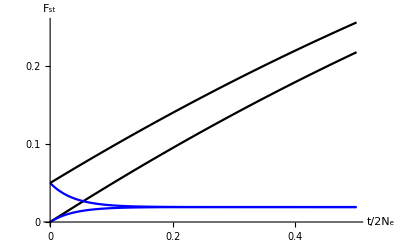

```mathematica
Plot[{Fst[T,0,2],Fst[T,6.4,2],Fst[T,0,2,0.05],Fst[T,6.4,2,0.05]},{T,0,0.5},PlotStyle->{Black,Blue},AxesLabel->{"t/2N_e","F_st"},BaseStyle->{FontFamily->"Times",FontSize->14},Ticks->{{0,0.2,0.4},{0,0.1,0.2}}]
```

### Barrier to gene flow due to linked loci: one deme

Selection on linked loci reduces the effective rate of immigration by a factor that depends on the relative rates of recombination and selection. Barton and Bengtsson (1986, Eq. A6) give a general recursion for the reduction in the effective rate of gene flow, for an arbitrary number of selected loci, assuming weak selection and recombination, and a low rate of flow into each deme, so that only the marginal (additive) effects of sets of alleles need be considered.  Multiple crossovers are ignored in this continuous-time limit..

A single selected locus, with selective disadvantage s>>m in the focal population, will reach equilibrium frequency m/s. The effective rate of influx of neutral alleles is then reduced to:

m_eff/m = r/(s+r)

For two loci, under selection s_1, s_2, with no epistasis, and a neutral locus in-between:

m_eff/m = r_1/(s_1+r_1)r_2/(s_2+r_2)

This is just the product of effects of each locus separately.  For a neutral locus to the left of selected locus 1, recombining at rates r_1, r_2=r_1+r_(1,2) with the two selected loci:

m_eff/m = r_1/(s_1+r_1)(r_2+s_1)/(s_1+s_2+r_2)

This is the product of the effects of the two loci, but with the recombination rate with the second locus, r_2, replaced by r_2+s_1. Thus, the effect of the second locus on gene flow is reduced by an increase in the effective recombination rate.  When selection is strong relative to recombination, this greatly weakens the effect of the barrier outside the two loci, relative to that between them.

The effect of the reduction in effective rate of gene flow on coalescence times and on F_st can be found by rescaling M=2 N_e m in the previous section.

### Barrier to gene flow due to two linked loci: one dimension

The barrier to flow of genes past two linked clines can be found using the general methods described by Barton and Bengtsson (1986). Although the solution can be written as a set of coupled differential equations, it is simpler to make numerical calculations using a discrete haploid stepping-stone model, with migration m=1/2 between adjacent demes. We assume negative frequency-dependent selection s at two loci, equivalent to selection against heterozygotes in diploids. First, the equilibrium frequencies of the four haploid genotypes g={g_00,g_01, g_10, g_11} are determined; at the boundaries, genotypes 00, 11 respectively are almost fixed.  Next, a linear recursion is derived for the frequencies u_i={u_(i,00),u_(i,01), u_(i,10), u_(i,11)} of a neutral allele within each background, in each deme, i. If the neutral allele frequencies at either end, u_1, u_n are fixed, then the solution settles to a form with a net step, Δu, due to the barrier; the barrier strength is defined by B=Δu/u'_00, where u'_1 is the gradient in allele frequency at the left. (Since the model is symmetric, u'_1 on the left equals u'_n on the right).

Given the haplotype frequencies, g_00,…, we need to know the matrix that determines the flow of neutral alleles between locations and between genetic backgrounds, due to migration and recombination.  Migration is straightforward. Denoting the vector of haplotype frequencies at deme i by g_i:

u_i^*=((m/2)(g_(i+1)u_(i+1)+g_(i-1)u_(i-1))+(1-m)g_i u_i)/((m/2)(g_(i+1)+g_(i-1))+(1-m)g_i)

At the left edge (i=1):

u_1^*=((m/2)g_2 u_2+(1-m/2)g_1 u_1)/((m/2)g_2+(1-m/2)g_1)

and similarly at the right. The effect of recombination can be written in matrix form as u_i^*=R.u_i:

R=(1-r_2 g_01-r_1 g_10-r_1 r_2 g_11 | r_2 g_01 | r_1 g_10 | r_1 r_2 g_11
r_2 g_00 | 1-r_2 g_00-r_1 r_2 g_10-r_1 g_11 | r_1 r_2 g_10 | r_1 g_11
r_1 g_00 | r_1 r_2 g_01 | 1-r_1 g_00-r_1 r_2 g_01-r_2 g_11 | r_2 g_11
r_1 r_2 g_00 | r_1 g_01 | r_2 g_10 | 1-r_1 r_2 g_00-r_1 g_01-r_2 g_10)

The matrices M, R representing migration and recombination are applied in the appropriate order; if the life cycle is select→recombine→migrate, we have u^*=M.R.u.  Now, suppose that we fix u_(1,00)={0,0,0,0} and u_(n,11)={0,0,0,1}.  Then, u_i=(M.R)_ij u_j+(M.R)_in u_n  and so u_i=(I-(M.R)^*)_ij^-1(M.R)_in u_n, where the matrix operations only include demes 2,…,(n-1). Code for the calculations are given in the accompanying Mathematica notebook.

#### Barriers between two demes, and in one-dimension, extend over a map distance r~s

Figure Sx compares the strengths of the barrier to gene flow between two demes with the barrier across a one-dimensional habitat, given two tightly linked loci.  The barrier to flow in the region between the selected loci is very strong (B/σ>1000, m_eff/m<0.005), because two recombination events are needed to transfer a neutral allele from on background to the other.  Outside the selected region, the barrier rapidly weakens, but remains substantial for a considerable distance (B/σ>20, m_eff/m<0.25 ~2cM away); this is because the scale of the barrier’s effect is r~s, which here is 5%.

This seems inconsistent with the data, which show an increase in F_st only immediately around the ROS/EL region (Fig. x). One explanation could be that selection on ROS and EL is weak (s~0.5%), so that the barrier has an effect only over this short map distance.  However, it seems highly unlikely that the effect of a major change in flower colour should be so small.  We have evidence that the difference between striatum and pseudomajus substantially affects pollinator preferences both in the field and in artificial arrays (Ellis, 2015), and the narrow clines at ROS and EL also suggest strong selection.

Figure Sx. Strengths of the barrier to gene flow between two demes (blue) and in one dimension (red), plotted across the genetic map.  There are two selected loci, each with divergence maintained by selection of strength s=0.05, and at positions 0, 0.005 on the genetic map (i.e., they are 0.5cM apart). The barrier to flow between two demes is represented as 5m/m_eff, a scaling which makes the barriers comparable in strength.

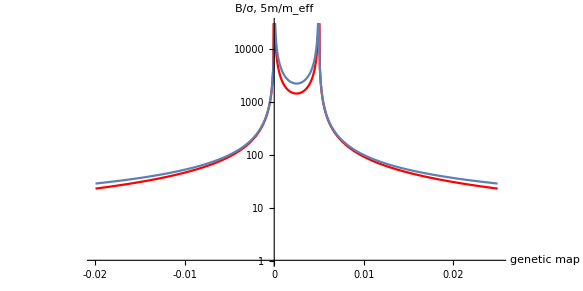

```mathematica
pln=pSol[0.5,0.005,0.05,0,20,100];
δ=0.0001;ϵ=10^-5;pr={{-0.02,0.025},{1,3 10^4}};
tt=Table[{r,If[Abs[r]<10^-5∨Abs[r-0.005]<10^-5,10^6,barrier2[r,0.5,0.005,pln⟦-1⟧]]/√0.5},{r,-0.02,0.025,δ}];
Show[ListLogPlot[tt,PlotRange->pr,Joined->True,BaseStyle->{FontFamily->"Times",FontSize->12},AxesLabel->{"genetic\nmap","B/σ, 5m/m_eff"},Ticks->{{-0.02, -0.01,0,0.01,0.02},{10,100,1000,10^4}},AspectRatio->0.5,PlotStyle->Red],
Show[LogPlot[5/Meff[r,0.005,0.05],{r,-0.02,0.025},PlotRange->pr]]]
```

An alternative explanation is that while the strong barrier in-between  ROS and EL inflates F_st, as observed, the weaker barrier outside ((B/σ<100, m_eff/m>0.05, say) does not.  Figure Sx shows the effect of the barrier shown in Fig.Sy (above) on F_st.  For flow between two discrete demes (upper blue line), the effect does spread widely across the genetic map.  However, immediately on either side of a barrier in a one-dimensional habitat (lower red line), the effect falls away much more quickly, as observed. This calculation was made on the assumption that a homogeneous population (in two demes or in one dimension) began diverging at some time in the past (e.g., following the last glaciation).  Making different assumptions about the initial state - for example, that there was some initial divergence following secondary contact - does not alter the local effect of the barrier that is depicted in Fig. Sx.

Figure Sx. Comparison between the effects of a barrier on F_st between two demes (blue), and immediately on either side of a barrier in one dimension (red). Two loci, each under selection s=0.05, and r=0.5cM apart, are assumed. For one dimension, values are for 200 demes, each of 150 diploid individuals, with a reduction in gene flow between demes 100, 101; results are shown at 2000 generations.  For flow between two demes (blue), N_e m=6.4, and T=0.5 N_e. Here, F_st is calculated by comparing the probability of coalescence more recently than 2000 generations, between two genes on different sides of the barrier, P_b, with that between two genes from within the same location, P_w.  Assuming that lineages that do not coalesce in this recent interval share ancestry much further back, F_st=(P_w-P_b)/(P_w+P_b).  The probability of coalescence before time t between genes in demes i, j, P_(t,i,j), is calculated from the recursion P-t+1 = ℐ/(2N) + (1 - ℐ/(2N)) M.P_t.M^T, where ℐ is the identity matrix, and M the migration matrix, which includes the effects of the barrier. The code is given in the accompanying Mathematica notebook.

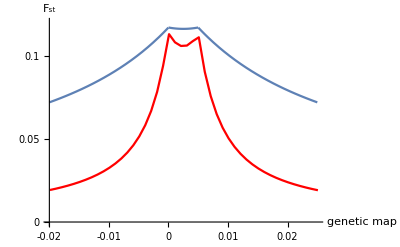

```mathematica
Show[Plot[Fst[0.25,6.4Meff[r,0.005,0.05],2],{r,-0.02,0.025},PlotRange->{{-0.02,0.025},{0,0.12}}],ListLinePlot[tbl[20,300.,{100,101},0.02],PlotStyle->Red],AxesLabel->{"genetic\nmap","F_st"},BaseStyle->{FontFamily->"Times",FontSize->14},Ticks->{{-0.02,-0.01,0,0.01,0.02},{0,0.05,0.10}},AxesOrigin->{-0.02,0}]
```

## Working

### Flow between two demes

#### From B&B A6

This is the recursion from Barton and Bengtsson (1986), correcting the typos (the summation index i was written as 1), and generalised to allow for arbitrary selection and recombination. Both are assumed weak, and selection is additive.  The frequencies of neutral alleles associated with j selected loci to the left, and k to the right, are u_(j,k).  Selection coefficients are labelled s_i, and recombination rates r_i; the set of loci to the left is 𝒥, and to the right, 𝒦, with the number of such genes defined as J=|𝒥|, K=|𝒦|. The crucial assumption is that only single crossovers need be considered, so that a neutral allele is always associated with a contiguous set of selected alleles to the left and rightThere is a slow influx of neutral alleles at rate mΔu, where Δu is the difference in allele frequencies between populations; the system reaches a quasi-steady state in which the rates of change of neutral alleles in the various backgrounds is zero (δu_(j,k)=0 for j>0, k>0), except for neutral alleles that have reached the native background; m_eff/m=(δu_(0,0))/Δu.  This leads to the closed recursions, a generalisation of Eq. A6 (Barton and Bengtsson, 1986):

δu_(J,K)=0=m Δu-(∑_(i∈𝒥,𝒦) s_i+r_(𝒥,𝒦) )u_(J,K)
δu_(j,k)=0=-(∑_(i∈𝒿,𝓀) s_i+r_(𝒥,𝒦) )u_(𝒿,𝓀)+(∑_(i>j) r_(𝒾,𝓀)u_(i,k)+∑_(i>k) r_(𝒾,𝓀)u_(j,i))
0=δu_(0,k)=-(s k-r(k-α))u_(0,k)+r(α∑_(i>0) u_(i,k)+∑_(i>k) u_(0,i))
0=δu_(j,0)=-sj u_(j,0)-r(j-1+α)u_(j,0)+r(∑_(i>j) u_(i,0)+(1-α)∑_(i>0) u_(j,i))
δu_(0,0)=r(α∑_(i>0) u_(i,0)+(1-α)∑_(i>0) u_(0,i))

```mathematica
Clear[u];
u[α_,θ_,J_,K_][j_,k_]:=u[α,θ,J,K][j,k]=Module[{i},
If[j==J∧k==K,1/((J+K)(θ+1)-1),
If[j==0,If[k==0,
α∑_(i=1)^J u[α,θ,J,K][i,0]+(1-α)∑_(i=1)^K u[α,θ,J,K][0,i],
(α∑_(i=1)^J u[α,θ,J,K][i,k]+∑_(i=k+1)^K u[α,θ,J,K][0,i])/(k(θ+1)-α)],
If[k==0,
(∑_(i=j+1)^J u[α,θ,J,K][i,0]+(1-α)∑_(i=1)^K u[α,θ,J,K][j,i])/(j(θ+1)-(1-α)),
(∑_(i=j+1)^J u[α,θ,J,K][i,k]+∑_(i=k+1)^K u[α,θ,J,K][j,i])/((j+k)(θ+1)-1)]]]];
u[α_,θ_,J_][j_]:=If[j==J,1/(J(θ+1)-(1-α)),
If[j==0,
α∑_(i=1)^J u[α,θ,J][i],
(∑_(i=j+1)^J u[α,θ,J][i])/(j(θ+1)-(1-α))]];
```

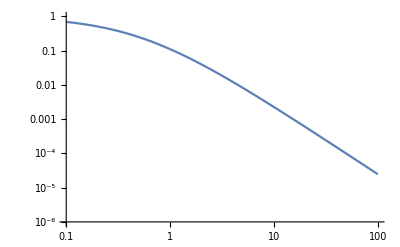

```mathematica
LogLogPlot[u[0.5,ϕ,1,1][0,0],{ϕ,0.1,100},AxesOrigin->{0.1,10^-6}]
```

```mathematica
u[α,ϕ,2][0]//Simplify
```

(α (1+α+ϕ))/((α+ϕ) (α+2 ϕ))

```mathematica
u11[α_,θ_]:=If[α<0,u[-α,θ,2][0],If[α>1,u[α-1,θ,2][0],u[α,θ,1,1][0,0]]];
```

```mathematica
u1[α_,θ_]:=u[Abs[α],θ,1][0];
```

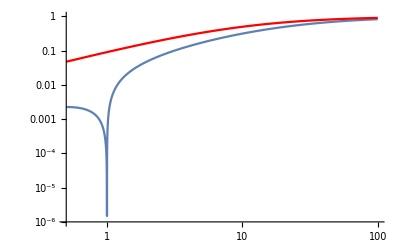

```mathematica
Show[LogLogPlot[u11[α,10],{α,0.5,100},AxesOrigin->{0.5,10^-6}],LogLogPlot[u1[α,10],{α,0.5,100},AxesOrigin->{0.5,10^-6},PlotStyle->Red]]
```

```mathematica
u[α,ϕ,2][0]//Simplify
```

(α (1+α+ϕ))/((α+ϕ) (α+2 ϕ))

#### Effect of a barrier on F_st

This shows Fst at T=0.25(2 N_e), with M=6.4, for s/r=1, 5, 20. A localised effect (left) implies weak selection s~r

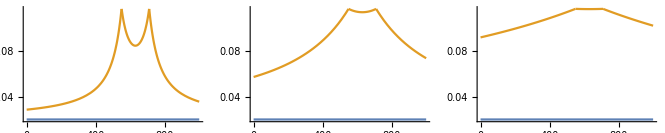

```mathematica
Show[GraphicsRow[Plot[{0.02,Fst[0.25,6.4u11[(x-550)/160,#],2]},{x,0,1000},AxesOrigin->{0,0},PlotRange->All]&/@{1,5,20}]]
```

The pattern with a single selected locus is similar

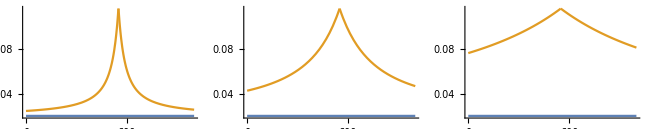

```mathematica
Show[GraphicsRow[Plot[{0.02,Fst[0.25,6.4u1[(x-550)/160,#],2]},{x,0,1000},AxesOrigin->{0,0},PlotRange->All]&/@{1,5,20}]]
```

### 1D barrier

#### Effect of a barrier on T_w, T_b - from B, 2008

From Barton (2008), we have a simple formula for the identity in state; L=σ/√(2μ):

F(x,x') = 1/(4ρσ √(2μ))(ⅇ^(-|x-x'|/L)+B/(2L+B)ⅇ^(-|x+x'|/L))     (same side)
F(x,x') = 1/(4ρσ √(2μ))(2L)/(2L+B)ⅇ^(-|x-x'|/L)    (different sides)

Now, the expected coalescence time is minus half the derivative of these expressions wrt μ at μ=0. However, we need the finite time versions, and we need not just the expected coalescence time, but the probability of coalescence in some time interval. It should be possible to calculate these analytically, but I have just iterated recursions numerically.

#### Analytical solution with no barrier

The scaled distribution of coalescence times for genes at the same place is:

1/(√(π  T))- ⅇ^T erfc[√T]=1/(√(π  T))- 2 ⅇ^T (1-Pr[√(2T)])    
where T = t/(4ρ σ)^2, erfc[x]=2/(√π)∫_x^∞ ⅇ^(-y^2)ⅆy, Pr[x]=∫_(-∞)^x (ⅇ^(-y^2/2))/(√(2π))ⅆy  which form to use?

There seems to be no explicit solution for genes in different places, though the LT is rather simple:

```mathematica
FullSimplify[InverseLaplaceTransform[Exp[-Abs[x] √ω]/(1+√ω),ω,t],ρσ>0]
```

InverseLaplaceTransform[ⅇ^(-√ω Abs[x])/(1+√ω),ω,t]

The mean coalescence time for genes separated by x, and sampled uniformly,  is:

T_S= 2 N_tot+(x(L-x))/(2 σ^2)
T_T=2 N_tot+L^2/(12 σ^2)
F_st=(T_T-T_S)/T_T=(L^2-6x(L-x))/(24 σ^2 N_tot+L^2)

which can be negative.  Note that this is quite different from F_st defined for local fluctuations,  because it depends strongly on large-scale  effects.

#### Scalings etc

This is the relation between the reduction in gene flow, θ, and the barrier, in a stepping-stone model:

B/σ=1/(√m)(1/θ-1) so θ=1/(1+√m(B/σ))

In a 1D habitat, the dimensionless scalings are:

T=t/(4ρσ)^2      X=x/(4ρ σ^2)

#### Expected coalescence time with no barrier

I could calculate F_(i,j) in a stepping-stone model. However I can also calculate the expected coalescence time T_(t,i,j) directly, which may be more direct.  In the absence of a barrier, this depends only on the separation:

T_(0,i)=0
T_(t+1,i)=T_(t,i)^*(1-δ_i/(2n))
T_(t,0)^*=1+T_(t,0)((1-m)^2+m^2/2)+T_(t,1)2m(1-m)+T_(t,2)m^2/2
T_(t,1)^*=1+T_(t,1)((1-m)^2+m^2/2)+T_(t,0)m(1-m)+T_(t,2)m(1-m)+T_(t,3)m^2/2
T_(t,i)^*=1+T_(t,i)((1-m)^2+m^2/2)+m(1-m)(T_(t,i-1)+T_(t,i+1))+m^2/4(T_(t,i-2)+T_(t,i+2))

Note that this does not approach the analytical solution above, because it is on an infinite range and for a finite time.

```mathematica
Clear[expT];
expT[0,_,_,_]:=0;
expT[t_,i_Integer,m_,n_]:=expT[t,i,m,n]=If[i<0,expT[t,-i,m,n],1+(1-KroneckerDelta[i]/(2n))(((1-m)^2+m^2/2)expT[t-1,i,m,n]+m(1-m)(expT[t-1,i+1,m,n]+expT[t-1,i-1,m,n])+m^2/4(expT[t-1,i+2,m,n]+expT[t-1,i-2,m,n]))];
```

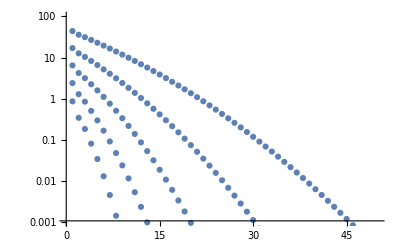

```mathematica
Show[ListLogPlot[Table[#-expT[#,i,0.5,10]+10^-6,{i,0,50}],PlotRange->{{0,50},{0.001,100}}]&/@{10,20,40,80,160}]
```

#### Numerical solution for T with a barrier - recursions

Suppose that between demes 0 and 1, migration is reduced from m/2 to m/2 θ, corresponding to B=(1/θ-1)ϵ.

T_(0,i,j)=0
T_(t+1,i,j)=T_(t,i,j)^*(1-(δ_(i,j))/(2n))
T_(t,i,j)^*=1+T_(t,i,j)(1-m)^2+m/2(1-m)(T_(t,i-1,j)+T_(t,i+1,j)+T_(t,i,j-1)+T_(t,i,j+1))+m^2/4(T_(t,i-1,j-1)+T_(t,i+1,j-1)+T_(t,i-1,j+1)+T_(t,i+1,j+1))    i,j≠0, 1
T_(t,0,j)^*=1+T_(t,0,j)(1-m)(1-m(1+θ)/2)+m/2(1-m)(T_(t,-1,j)+θ T_(t,1,j))+m/2(1-m(1+θ)/2)(T_(t,0,j-1)+T_(t,0,j+1))+m^2/4(T_(t,-1,j-1)+θ T_(t,1,j-1)+T_(t,-1,j+1)+θ T_(t,1,j+1))      j≠0,1
and similarly for i=1, and j=0, 1, i≠0,1
T_(t,0,0)^*=1+T_(t,0,0)(1-m(1+θ)/2)^2+m/2(1-m(1+θ)/2)(T_(t,0,-1)+θ T_(t,0,1)+T_(t,-1,0)+θ T_(t,1,0))+m^2/4(T_(t,-1,-1)+θ T_(t,1,-1)+θ T_(t,-1,+1)+θ^2 T_(t,1,1))      j≠0,1
T_(t,0,1)^*=1+T_(t,0,1)(1-m(1+θ)/2)^2+m/2(1-m(1+θ)/2)(T_(t,0,2)+θ T_(t,0,0)+T_(t,-1,1)+θ T_(t,1,1))+m^2/4(T_(t,-1,2)+θ T_(t,1,2)+θ T_(t,-1,0)+θ^2 T_(t,1,0))      j≠0,1

This can be rewritten more compactly as:

M^0={m/2,1-m,m/2}      M^L={m/2 θ,1-m((1+θ)/2),m/2}    M^R={m/2,1-m((1+θ)/2),m/2 θ}
T_(t,i,j)^*=1+∑_(x=-1)^1 ∑_(y=-1)^1 M_x^0 M_y^0 T_(t,i+x,j+y)         i,j≠0, 1
T_(t,0,j)^*=1+∑_(x=-1)^1 ∑_(y=-1)^1 M_x^R M_y^0 T_(t,i+x,j+y)             j≠0,1
and similarly for i=1, and j=0, 1, i≠0,1
T_(t,0,0)^*=1+∑_(x=-1)^1 ∑_(y=-1)^1 M_x^R M_y^R T_(t,i+x,j+y)             j≠0,1
T_(t,0,1)^*=1+∑_(x=-1)^1 ∑_(y=-1)^1 M_x^R M_y^L T_(t,i+x,j+y)      j≠0,1

I calculate this by storing T on some range, and padding with no gene flow at the left and right edges.

#### Example: 200 demes, 2N=10, 2000 generations, T with & without a barrier θ=0.01

```mathematica
Tl=NestList[iterT[0.5,10.,0.01,100,100],ConstantArray[0,{200,200}],20];
Tl0=NestList[iterT[0.5,10.,1,100,100],ConstantArray[0,{200,200}],20];
```

This shows T_max-T, for x=60,…,100, at T_max=2000. The standard increase in coalescence time as genes get further apart is evident at left; superimposed on this is a sharp increase in coalescence time across the barrier. Indeed, with this strength of barrier there has been rather little gene flow over 2000 generations

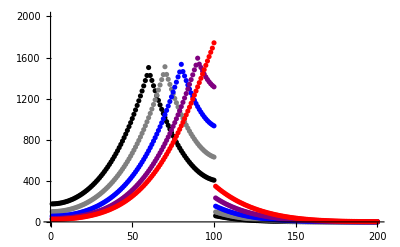

```mathematica
Show[MapThread[ListPlot[2000-Tl⟦-1,#1⟧,PlotStyle->#2,PlotRange->{{0,200},{0,2000}}]&,{{60,70,80,90,100},{Black,Gray,Blue,Purple,Red}}]]
```

This shows F_st against separation, with x, x' symmetrically placed.  With no barrier, this seems to converge to an asymptotic form

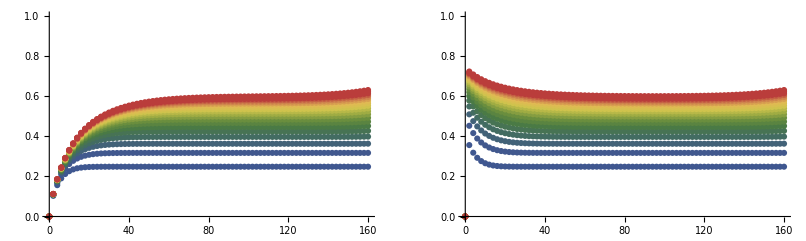

```mathematica
cf=ColorData["DarkRainbow"];
fst[T_,y_,t_]:=Table[Tw=(T⟦t+1,y-x,y-x⟧+T⟦t+1,y+x,y+x⟧)/2;Tb=T⟦t+1,y-x,y+x⟧;{2x,(Tb-Tw)/(Tb+Tw)},{x,0,80}];Show[GraphicsRow[{Show[Table[ListPlot[fst[Tl0,100,t],PlotStyle->cf[t/20],PlotRange->{{0,160},{0,1}}],{t,1,20}]],Show[Table[ListPlot[fst[Tl,100,t],PlotStyle->cf[t/20],PlotRange->{{0,160},{0,1}}],{t,1,20}]]}]]
```

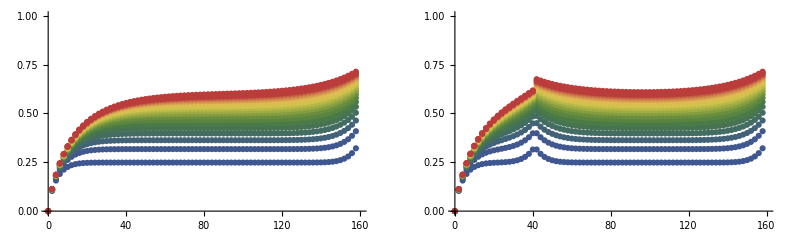

```mathematica
cf=ColorData["DarkRainbow"];
fst[T_,y_,t_]:=Table[Tw=(T⟦t+1,y-x,y-x⟧+T⟦t+1,y+x,y+x⟧)/2;Tb=T⟦t+1,y-x,y+x⟧;{2x,(Tb-Tw)/(Tb+Tw)},{x,0,Min[y-1,201-y]}];Show[GraphicsRow[{Show[Table[ListPlot[fst[Tl0,80,t],PlotStyle->cf[t/20],PlotRange->{{0,160},{0,1}}],{t,1,20}]],Show[Table[ListPlot[fst[Tl,80,t],PlotStyle->cf[t/20],PlotRange->{{0,160},{0,1}}],{t,1,20}]]}]]
```

This shows how T_w, T_b change through time, with & without a barrier. The two points are placed symmetrically at ±x. T_w increases with time, but more slowly, and would eventually converge.  With a barrier, T_w is smaller near the barrier because genes are confined in a smaller space.

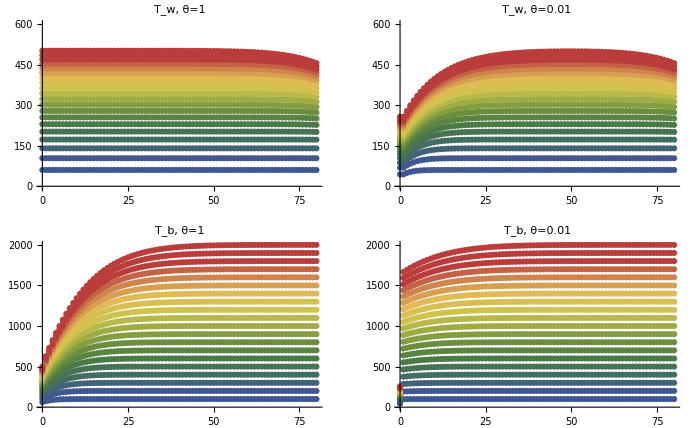

```mathematica
grx[T_,a_,r_,lb_]:=Show[Table[ListPlot[Table[{x,T⟦t+1,100+a x,100+x⟧},{x,0,80}],PlotStyle->cf[t/20],PlotRange->{{0,80},{0,r}},PlotLabel->lb],{t,1,20}]];
Show[GraphicsGrid[{{grx[Tl0,1,600,"T_w, θ=1"],grx[Tl,1,600,"T_w, θ=0.01"]},{grx[Tl0,-1,2000,"T_b, θ=1"],grx[Tl,-1,2000,"T_b, θ=0.01"]}}]]
```

This compares the final F_st against separation, with and without a barrier, at 2000 generations. Note that

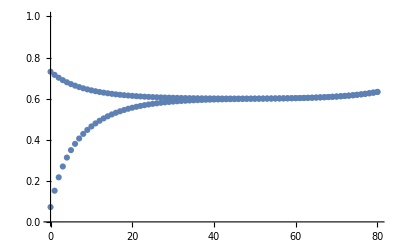

```mathematica
Show[ListPlot[fst[#,20],PlotStyle->cf[t/20],PlotRange->{{0,80},{0,1}}]&/@{Tl0,Tl}]
```

#### Numerical solution for P with a barrier - recursions

We can calculate the probability of coalescence before time T_max in a similar way. This can be written compactly as:

M^0={m/2,1-m,m/2}      M^L={m/2 θ,1-m((1+θ)/2),m/2}    M^R={m/2,1-m((1+θ)/2),m/2 θ}
P_(0,i,j)=0
P_(t+1,i,j)=(δ_(i,j))/(2n)+P_(t,i,j)^*(1-(δ_(i,j))/(2n))
P_(t,i,j)^*=∑_(x=-1)^1 ∑_(y=-1)^1 M_x^0 M_y^0 P_(t,i+x,j+y)         i,j≠0, 1
P_(t,0,j)^*=∑_(x=-1)^1 ∑_(y=-1)^1 M_x^R M_y^0 P_(t,i+x,j+y)             j≠0,1
and similarly for i=1, and j=0, 1, i≠0,1
P_(t,0,0)^*=∑_(x=-1)^1 ∑_(y=-1)^1 M_x^R M_y^R P_(t,i+x,j+y)             j≠0,1
P_(t,0,1)^*=∑_(x=-1)^1 ∑_(y=-1)^1 M_x^R M_y^L P_(t,i+x,j+y)      j≠0,1

I calculate this by storing P on some range, and padding with no gene flow at the left and right edges.

#### Example: 200 demes, 2N=100, 2000 generations, P with & without a barrier θ=0.01

```mathematica
Pl=NestList[iterP[0.5,100.,0.01,100,100],ConstantArray[0,{200,200}],20];
Pl0=NestList[iterP[0.5,100.,1,100,100],ConstantArray[0,{200,200}],20];
```

This shows P, for x=60,…,100, at T_max=2000. The decreasing probability of coalescence as genes get further apart is evident at left; superimposed on this is a sharp drop in probability across the barrier. Indeed, with this strength of barrier there has been rather little gene flow over 2000 generations

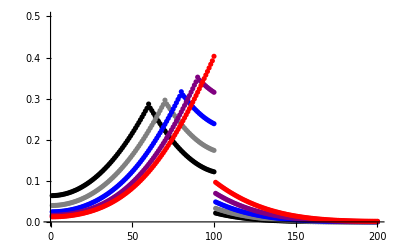

```mathematica
Show[MapThread[ListPlot[Pl⟦-1,#1⟧,PlotStyle->#2,PlotRange->{{0,200},{0,0.5}}]&,{{60,70,80,90,100},{Black,Gray,Blue,Purple,Red}}]]
```

This shows P against separation, with x, x' symmetrically placed.  This seems to converge to an asymptotic form. Top: no barrier, bottom: θ=0.01. Columns: x, x' centred at 100, 120, 140.

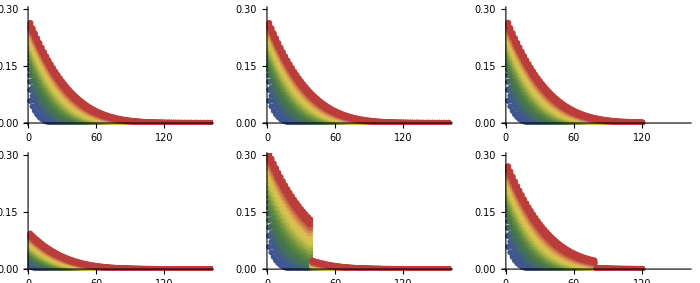

```mathematica
cf=ColorData["DarkRainbow"];
pr[P_,y_,t_]:=Table[{2x,P⟦t+1,y-x,y+x⟧},{x,1,Min[200-y,y-1]}];Show[GraphicsGrid[Outer[Show[Table[ListPlot[pr[#1,#2,t],PlotStyle->cf[t/20],PlotRange->{{0,160},{0,0.3}}],{t,1,20}]]&,{Pl0,Pl},{100,120,140},1]]]
```

#### Effect of a barrier on F_st

Assume that at some time T_m in the past, a homogeneous population colonises a 1D habitat; it then diverges in the presence of a barrier. Alternative scenarios could be secondary contact between two populations that are already somewhat divergent, or primary divergence in a 1D population that is at equilibrium. However, note that i) the population was not at its present location ~10^4generations ago, and ii) we may approximate the history before T_m as homogeneous, since lineages will have diffused widely by then.  As a check, results should not be sensitive to assumptions about that history.

Let T̃ be the expected time to coalescence, tracing only back to T_m (which is what I calculate). Then, the actual expected time, T_x, is this, plus the contribution (1-P_x)T_A from the ancestral population. For T_A large, this implies that T_x is dominated by P_x, and in particular, that F_st between two populations is (T_x-T_0)/(T_x+T_0)~(P_0-P_x)/(2-P_0-P_x):

(T̃)_x=(1-P_x)T_m+P_x T_(x,c)
T_x=(1-P_x)(T_A+T_m)+P_x T_(x,c) =(1-P_x)T_A +(T̃)_x

This sets up solutions with and without a barrier θ=0.01, with 2N=100

```mathematica
Pl=NestList[iterP[0.5,100.,0.01,100,100],ConstantArray[0,{200,200}],20];
Pl0=NestList[iterP[0.5,100.,1,100,100],ConstantArray[0,{200,200}],20];
```

This shows the increase in F_st over time, between demes centred at 100, 80 (top, bottom), separated by 10, 20, 30 (left, right), with a barrier θ=0.01 right of deme 100; 2N=100.  Note that the F_st with a barrier grows independently of the location (more or less), but without a barrier, we do see IBD.

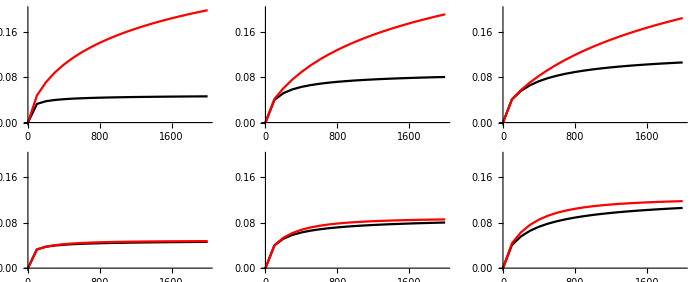

```mathematica
gra[{x_,y_}][P_,c_]:=ListLinePlot[Transpose[{Range[0,2000,100],((P⟦All,x,x⟧+P⟦All,y,y⟧)/2-P⟦All,x,y⟧)/(2-((P⟦All,x,x⟧+P⟦All,y,y⟧)/2+P⟦All,x,y⟧))}],PlotStyle->c,PlotRange->{{0,2010},{0,0.2}}];Show[GraphicsGrid[Outer[Show[MapThread[gra[#1+{-#2,#2}],{{Pl0,Pl},{Black,Red}}]]&,{100,80},{5,10,15},1]]]
```

From “Table of results...” in “Ros-El May 19 2017”, it seems that there is an increase in F_st with distance both inside and outside Ros/El, but only when one compares {1,8} with the rest.  Given that (from these limited samples) there is no clear IBD, it may be best to just look at the one pair, and treat the F_st away from Ros/El as a residue from secondary contact (?). 

region | kb | pools |  F_st | π_1 | π_2 | π_w | π_b
left of Ros, right of El | 487 | 4,5 | 0.019 | 0.0104 | 0.0102 | 0.0103 | 0.0107
  |   | 3,6 | 0.019 | 0.0104 | 0.0102 | 0.0103 | 0.0107
  |   | 1,8 | 0.052 | 0.0113 | 0.0104 | 0.0108 | 0.0120
between Ros/El A,B | 104 | 4,5 | 0.125 | 0.0088 | 0.0096 | 0.0092 | 0.0119
  |   | 3,6 | 0.096 | 0.0097 | 0.0092 | 0.0093 | 0.0114
  |   | 1,8 | 0.204 | 0.0084 | 0.0087 | 0.0086 | 0.0129

F_st vs r at times T_m=500, 1000, 2000, with 2ρ=300, or ρσ~100.  Left: immediately either side of a barrier; right: demes 90, 111 (i.e. ±14σ).  F_st increases with time, and is quite localised.

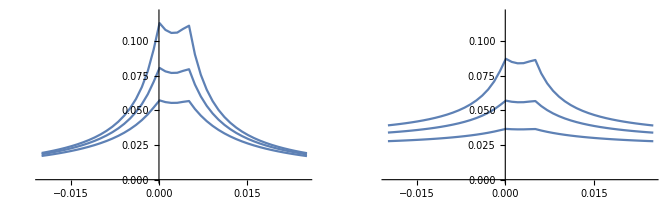

```mathematica
tbl[t_,n_,{x_,y_},rm_]:=Table[{r,fstP[ProbCoal[barrier2[r,0.5,0.005,pln⟦-1⟧],n,2000]⟦t+1⟧,{x,y}]},{r,-rm+0.0001,rm+0.0051,0.001}];
Show[GraphicsRow[{
Show[ListLinePlot[tbl[#,300.,{100,101},0.02],PlotRange->{{-0.02,0.025},{0,0.12}}]&/@{5,10,20}],
Show[ListLinePlot[tbl[#,300.,{90,111},0.02],PlotRange->{{-0.02,0.025},{0,0.12}}]&/@{5,10,20}]}]]
```

Comparison between the effects of a barrier on F_st between two demes (blue), and in 1D (red). The effect of the barrier on F_st declines much more sharply away from ROS/EL in 1D than when there is a single deme.  Two loci, each under selection s=0.05, and r=0.5cM apart, are assumed. For one dimension, values are for 200 demes of 150 diploid individuals, with a reduction in gene flow between the two central demes; results are shown at 2000 generations.  For flow between two demes, N_e m=6.4, and T=0.5 N_e.

```mathematica
Show[Plot[Fst[0.25,6.4Meff[r,0.005,0.05],2],{r,-0.02,0.025},PlotRange->{{-0.02,0.025},{0,0.12}}],ListLinePlot[tbl[20,300.,{100,101},0.02],PlotStyle->Red],AxesLabel->{"genetic\nmap","F_st"},BaseStyle->{FontFamily->"Times",FontSize->14},Ticks->{{-0.02,-0.01,0,0.01,0.02},{0,0.05,0.10}},AxesOrigin->{-0.02,0}]
```

-Graphics-

## Definitions

### Expected T, P in 1D

#### mig

```mathematica
mig::usage="mig[x,m] returns {m/2,1-m,m/2} according to x=-1,-0,1. mig[x,m,θ,Left] returns {mθ/2,1-m(1+θ)/2,m/2}, mig[x,m,θ,Right] returns {m/2,1-m(1+θ)/2,mθ/2}";
```

```mathematica
mig[x:(-1|0|1),m_]:=(1-m)(1-Abs[x])+m/2 Abs[x];
mig[0,m_,θ_,Left|Right]:=1-m((1+θ)/2);
mig[-1,m_,θ_,Left]:=m/2 θ;mig[1,m_,θ_,Left]:=m/2;
mig[-1,m_,θ_,Right]:=m/2;mig[1,m_,θ_,Right]:=m/2 θ;
```

#### pad

```mathematica
pad::usage="pad[2][M] pads the four edges of a 2D array by copying the edge elements. pad[1][M] pads a 1D array.";
```

```mathematica
pad[1][M_List]:=Prepend[Append[M,M⟦-1⟧],M⟦1⟧];
pad[2][M_List]:=Transpose[pad[1][Transpose[pad[1][M]]]];
```

#### shift

```mathematica
shift::usage="shift[{i,j}][M] rotates a 2D array by {i,j}; the new element {x,y} is the old {x+i,y+j}. shift[i][M] rotates a 1D array by {i}; the new element x is the old x+i";
```

```mathematica
shift[{i_Integer,j_Integer}][M_List]:=Transpose[RotateLeft[Transpose[RotateLeft[M,i]],j]];
shift[i_Integer][M_List]:=RotateLeft[M,i];
```

#### padShift

```mathematica
padShift::usage="padShift[{i,j}][M] pads the edges, makes the shift, and deletes the edges. i,j must be -1|0|1. padShift[i][M] does the same in 1D";
```

```mathematica
padShift[{i:(-1|0|1),j:(-1|0|1)}][M_List]:=(shift[{i,j}][pad[2][M]])⟦2;;-2,2;;-2⟧;
padShift[i:(-1|0|1)][M_List]:=(shift[i][pad[1][M]])⟦2;;-2⟧;
```

#### iterT

```mathematica
iterT::usage="iterT[m,n][T] iterates a 2D array for the expected coalescence time through one generation. iterT[m,n,θ,k_b][T] includes a barrier that reduces gene flow by a factor θ between k_b and k_b+1. iterT[m,n,θ,k_b,j][T] iterates through j timesteps.";
```

```mathematica
iterT[m_,n_][T_List]:=Module[{k=Length[T]},
(1-IdentityMatrix[k]/n)(1+Total[Outer[(mig[#1,m]mig[#2,m]padShift[{##}][T])&,{-1,0,1},{-1,0,1}],2])];
```

```mathematica
iterT[m_,n_,θ_,kb_Integer][T_List]:=Module[{k=Length[T],x,T0,T1},
T0=Sum[padShift[x][T]mig[x,m],{x,-1,1}];
T0=Transpose[ReplacePart[T0,
{kb->Sum[T⟦kb+x⟧mig[x,m,θ,Right],{x,-1,1}],
kb+1->Sum[T⟦kb+1+x⟧mig[x,m,θ,Left],{x,-1,1}]}]];
T1=Sum[padShift[x][T0]mig[x,m],{x,-1,1}];
T1=Transpose[ReplacePart[T1,
{kb->Sum[T0⟦kb+x⟧mig[x,m,θ,Right],{x,-1,1}],
kb+1->Sum[T0⟦kb+1+x⟧mig[x,m,θ,Left],{x,-1,1}]}]];

(1-IdentityMatrix[k]/n)(1+T1)];
```

```mathematica
iterT[m_,n_,j_Integer][T_List]:=Nest[iterT[m,n],T,j];
iterT[m_,n_,θ_,kb_Integer,j_Integer][T_List]:=Nest[iterT[m,n,θ,kb],T,j];
```

#### iterP

```mathematica
iterP::usage="iterP[m,n][P] iterates a 2D array for the cumulative probability of coalescence through one generation. iterP[m,n,θ,k_b][P] includes a barrier that reduces gene flow by a factor θ between k_b and k_b+1. iterP[m,n,θ,k_b,j][P] iterates through j timesteps.";
```

```mathematica
iterP[m_,n_][P_List]:=Module[{k=Length[P]},
IdentityMatrix[k]/n+(1-IdentityMatrix[k]/n)Total[Outer[(mig[#1,m]mig[#2,m]padShift[{##}][P])&,{-1,0,1},{-1,0,1}],2]];
```

```mathematica
iterP[m_,n_,θ_,kb_Integer][P_List]:=Module[{k=Length[P],x,P0,P1},
P0=Sum[padShift[x][P]mig[x,m],{x,-1,1}];
P0=Transpose[ReplacePart[P0,
{kb->Sum[P⟦kb+x⟧mig[x,m,θ,Right],{x,-1,1}],
kb+1->Sum[P⟦kb+1+x⟧mig[x,m,θ,Left],{x,-1,1}]}]];
P1=Sum[padShift[x][P0]mig[x,m],{x,-1,1}];
P1=Transpose[ReplacePart[P1,
{kb->Sum[P0⟦kb+x⟧mig[x,m,θ,Right],{x,-1,1}],
kb+1->Sum[P0⟦kb+1+x⟧mig[x,m,θ,Left],{x,-1,1}]}]];

IdentityMatrix[k]/n+(1-IdentityMatrix[k]/n)P1];
```

```mathematica
iterP[m_,n_,j_Integer][P_List]:=Nest[iterP[m,n],P,j];
iterP[m_,n_,θ_,kb_Integer,j_Integer][P_List]:=Nest[iterP[m,n,θ,kb],P,j];
```

### From “Barrier due to two loci 4.7.14”

#### chooseLoci

```mathematica
chooseLoci::usage="chooseLoci[{{p_(1, 1),…},…},k,{Δp_min,Δp_max}] lists those loci that have Δp in the specified range(Δp_min≤Δp<Δp_max); he difference is defined by he first and last k demes";
```

```mathematica
chooseLoci[p_List,k_Integer,{dp0_,dp1_}]:=Pick[Range[Length[p⟦1⟧]],(dp1>Abs[#]≥dp0)&/@Mean[p⟦-k;;-1⟧-p⟦1;;k⟧]];
```

#### fst

```mathematica
fst::usage="fst[{{p_(1, 1),…},…},δr] gives {{r_1,F_1},…}, estimating F_st along the map. The data are a matrix of allele frequencies, demes×loci, deleting indeterminate results. fst[{{p_(1, 1),…},…},{i_1,i_2,…},δr] uses a subset of loci";
```

```mathematica
fst[p_List,dr_]:=fst[p,All,dr];
fst[p_List,s_,dr_]:=Module[{mn,nl=Length[p⟦1⟧]},
DeleteCases[MapThread[{#1,mn=Mean[#2];If[mn≤0.∨mn≥1,Indeterminate,N[Variance[#2]/(mn(1-mn))]]}&,{Range[-(nl-1)dr/2,(nl-1)dr/2,dr],Transpose[p]}⟦All,s⟧],{_,Indeterminate}]];
```

#### countTypes

```mathematica
countTypes::usage="countTypes[{{0,0,…},…}] gives the numbers of {{0…},{1…},{…0,1…},{…1,0…},other}";
```

```mathematica
countTypes[s_List]:=Module[{cc},
cc={Count[s,{0...}],Count[s,{1...}],Count[s,{0..,1..}],Count[s,{1..,0..}]};Append[cc,Length[s]-Total[cc]]];
```

#### smooth

```mathematica
smooth[f_List,j_]:=Drop[Mean[RotateLeft[f,#]&/@Range[0,j]],-j];
```

#### breakPoint

```mathematica
breakPoint::usage="breakPoint[{0,0,…,1,1}] gives the positions of points where 0→1 and 1→0";
```

```mathematica
breakPoint[s_List]:=Flatten[Position[Drop[s-RotateLeft[s],-1],#]]&/@{-1,1};
```

#### convertInterval

```mathematica
convertInterval::usage="convertInterval[{x_0,x_1},k_sel,n_loci,δr] converts an interval on the genetic map, measured relative to the selected locus, # k_sel, to a set of loci that fall within that interval.";
```

```mathematica
convertInterval[{x0_,x1_},ksel_,nloci_,δr_]:=Max[1,Min[nloci,#]]&/@(Floor[(ksel+{-1,1}{x0,x1}/δr)]+{1,0});
```

#### p

```mathematica
p::usage="p[{x_00,x_01,x_10,x_11}] gives allele frequencies.  p[{x_00,…},…}] does the same for a cline";
```

```mathematica
p[x_List]:=x.{{0,0},{0,1},{1,0},{1,1}};
```

#### d

```mathematica
d::usage="d[{x_00,x_01,x_10,x_11}] gives LD.  d[{x_00,…},…}] does the same for a cline";
```

```mathematica
d[{x00_,x01_,x10_,x11_}]:=(x00 x11-x01 x10);
d[x:{___List}]:=d/@x;
```

#### select

```mathematica
select::usage="select[s,ℰ][x] applies selection to the four haplotype frequencies. select[s,ℰ][{x_1,…}] selects on a cline";
```

```mathematica
select[s_,ℰ_][{x00_,x01_,x10_,x11_}]:=Module[{nx},
nx={x00,x01,x10,x11}(1-ℰ{0,1,1,0})(1-s{x10+x11,x10+x11,x00+x01,x00+x01})(1-s{x01+x11,x00+x10,x01+x11,x00+x10});
nx/Total[nx]];
select[s_,ℰ_][x:{___List}]:=select[s,ℰ]/@x;
```

#### migrate

```mathematica
migrate::usage="migrate[m][x] applies migration to a cline; boundaries are at {1,0,0,0} and {0,0,0,1}";
```

```mathematica
migrate[m_][x:{___List}]:=Module[{nx=Append[Prepend[x,{1,0,0,0}],{0,0,0,1}]},
Drop[Drop[m/2(RotateLeft[nx]+RotateRight[nx])+(1-m)nx,1],-1]];
```

#### recombine

```mathematica
recombine::usage="recombine[r][x] applies recombination to genotype frequencies; recombine[s,ℰ][{x_1,…}] recombines on a cline";
```

```mathematica
recombine[r_][x:{_,_,_,_}]:=x-r{1,-1,-1,1}d[x];
recombine[r_][x:{___List}]:=recombine[r]/@x;
```

#### rMat

```mathematica
rMat::usage="rMat[{r_1,r_2},{g_00,g_01,g_10,g_11},s] gives the 4×4 matrix that determines flow between backgrounds. s=-1 indicates a neutral gene to the left, 0 inbetween, +1 on the right.  The intervals are always ordered left to right.";
```

```mathematica
rMat[{r1_,r2_},{g00_,g01_,g10_,g11_},0]:=Module[{nm},
nm=({{0, r2 g01, r1 g10, r1 r2 g11}, {r2 g00, 0, r1 r2 g10, r1 g11}, {r1 g00, r1 r2 g01, 0, r2 g11}, {r1 r2 g00, r1 g01, r2 g10, 0}});
DiagonalMatrix[1-(Total/@nm)]+nm];
```

```mathematica
rMat[{r1_,r2_},{g00_,g01_,g10_,g11_},-1]:=Module[{nm},
nm=({{0, r1(1-r2) g01, r1 g10, r1(1-r2)g11}, {r1(1-r2) g00, 0, r1(1-r2)  g10, r1 g11}, {r1 g00, r1 (1-r2)g01, 0, r1(1-r2) g11}, {r1(1-r2)g00, r1 g01, r1(1-r2) g10, 0}});
DiagonalMatrix[1-(Total/@nm)]+nm];
```

```mathematica
rMat[{r1_,r2_},{g00_,g01_,g10_,g11_},1]:=Module[{nm},
nm=({{0, r2 g01, (1-r1)r2 g10, (1-r1)r2g11}, {r2 g00, 0, (1-r1)r2   g10, (1-r1)r2  g11}, {(1-r1)r2 g00, (1-r1)r2 g01, 0, r2 g11}, {(1-r1)r2g00, (1-r1)r2 g01, r2 g10, 0}});
DiagonalMatrix[1-(Total/@nm)]+nm];
```

#### rMatCline

```mathematica
rMatCline::usage="rMatCline[{r_1,r_2},{{g_00,g_01,g_10,g_11},…},s] sets up a 4n×4n matrix that determines flow between backgrounds across a cline. s=-1, 0, 1 indicates the location of the neutral locus.";
```

```mathematica
rMatCline[{r1_,r2_},x_,s_]:=SparseArray[ArrayFlatten[Normal[SparseArray[{i_,i_}:>(rMat[{r1,r2},#,s]&/@x)⟦i⟧,{Length[x],Length[x]}]]]];
```

#### mMatCline

```mathematica
mMatCline::usage="mMatCline[m,{{g_00,…},…}] gives the migration matrix for a two-locus cline. mMatCline[m,n] gives the simple migration matrix.";
```

```mathematica
mMatCline[m_,n_Integer]:=SparseArray[{{1,1}->1-m/2,{2,2}->1-m/2,{3,3}->1-m/2,{4,4}->1-m/2,{4n-3,4n-3}->1-m/2,{4n-2,4n-2}->1-m/2,{4n-1,4n-1}->1-m/2,{4n,4n}->1-m/2,Band[{5,1}]->m/2,Band[{1,1}]->1-m,Band[{1,5}]->m/2},{4n,4n}];
```

```mathematica
mMatCline[m_,g_List]:=Module[{mat=mMatCline[m,Length[g]]},
Transpose[mat Flatten[g] ]/(mat.Flatten[g])];
```

#### initP

```mathematica
initP::usage="initP[n] sets up the initial population on {-n,n} demes";
```

```mathematica
initP[n_]:=Join[ConstantArray[{1,0,0,0},n],{{1,1,1,1}}/4,ConstantArray[{0,0,0,1},n]];
```

#### pSol

```mathematica
pSol::usage="pSol[m,r,s,ℰ,n,t_max] gives the solution for demes {-n,…,n}";
```

```mathematica
pSol[m_, r_,s_,ℰ_,nd_,tm_] := NestList[migrate[m][recombine[r][select[s,ℰ][#]]]&,initP[nd],tm];
```

#### uSol

```mathematica
uSol::usage="uSol[m,{r_1,r_2},{{g_00,…},…},s] estimates the equilibrium solution when u is fixed {0,1} at the ends; returns {{0,u_01,…},…,{…,u_10,1}}. s=-1, 0, 1 indicates the location of the neutral locus.";
```

```mathematica
uSol[m_, {r1_, r2_}, g_,s_] := Module[{fm, fm2},
   fm = mMatCline[m, g].rMatCline[{r1, r2}, g,s];
   fm2 = fm[[2 ;; -2, 2 ;; -2]];
   Partition[Join[{0}, Inverse[IdentityMatrix[Length[fm2]] - fm2].fm[[2 ;; -2, -1]], {1}], 4]];
```

#### barrier

```mathematica
barrier::usage="barrier[m,{r_1,r_2},{{g_00,…},…},s] estimates the barrier strength.  s=-1, 0, 1 indicates the location of the neutral locus.";
```

```mathematica
barrier[m_, {r1_, r2_}, g_,s_] := Module[{us=uSol[m,{r1,r2},g,s],bb},
  bb= 1/{us⟦2,1⟧-us⟦1,1⟧,us⟦-1,-1⟧-us⟦-2,-1⟧}-Length[us]+1;
If[Abs[(bb⟦1⟧-bb⟦2⟧)/(bb⟦1⟧+bb⟦2⟧)]>0.01,Print["discrepancy: B=",bb]];
Mean[bb]];
```

#### Rs

```mathematica
Rs::usage="Rss[r_tot,α] gives the value R such that recombination across intervals Rα and R(1-α) is r_tot";
```

```mathematica
Rs[rt_,α_]:=(1-√(1-4 rt α(1-α)))/(2 α(1-α));
```

```mathematica
Solve[rt==R(1-α(1-α)R),R]
```

{{R→(-1-√(1-4 rt α+4 rt α^2))/(2 (-α+α^2))},{R→(-1+√(1-4 rt α+4 rt α^2))/(2 (-α+α^2))}}

#### Pr

```mathematica
Pr::usage="Pr[x] is the integral of the standard Gaussian";
```

```mathematica
Pr[X_]:=1/2 (1+Erf[X/(√2)]);
```

#### uNeutral

```mathematica
uNeutral::usage="uNeutral[x/B,(σ/B)^2t] gives the cline in frequency of a neutral allele";
```

```mathematica
uNeutral[X_,θ_]:=If[X<0,Pr[X/(√θ)]-ⅇ^(2(θ-X))Pr[(X-2θ)/(√θ)],1-Pr[-X/(√θ)]+ⅇ^(2(θ+X))Pr[(-X-2θ)/(√θ)]];
```

```mathematica
{D[Pr[X/(√θ)]-ⅇ^(2(θ-X))Pr[(X-2θ)/(√θ)],{X,2}]/(2D[Pr[X/(√θ)]-ⅇ^(2(θ-X))Pr[(X-2θ)/(√θ)],θ]),(1-2(Pr[X/(√θ)]-ⅇ^(2(θ-X))Pr[(X-2θ)/(√θ)]))/D[Pr[X/(√θ)]-ⅇ^(2(θ-X))Pr[(X-2θ)/(√θ)],X]}/.{X->0,θ->1.5}
```

{1.,1.}

#### makeRandomP

```mathematica
makeRandomP::usage="makeRandomP[ϵ,n] makes n random draws from a distribution (pq)^-1, with ϵ<p<1-ϵ";
```

```mathematica
makeRandomP[ϵ_,n_]:=Module[{z0=Log[(1-ϵ)/ϵ]},
1/(1+Exp[-RandomReal[{-z0,z0},n]])];
```

#### makeRandomPair

```mathematica
makeRandomPair::usage="makeRandomPair[F,ϵ,n] makes n random pairs of allele frequencies from a base distribution (pq)^-1, ϵ<p<1-ϵ, with Fst between them";
```

```mathematica
makeRandomPair[f_,ϵ_,n_]:=Module[{α,pp=makeRandomP[ϵ,n]},
If[f==0,Transpose[{pp,pp}],
α=1/f-1;RandomReal[BetaDistribution[α  #,α(1-#)],2]&/@pp]];
```

#### makePops

```mathematica
makePops::usage="makePops[{p_1,…,p_n_loci},n_demes,n_loci] sets up an n_demes×n_inds array of genomes, according to the specified allele frequencies.";
```

```mathematica
makePops[pl_,nd_,ninds_]:=Transpose[RandomInteger[BernoulliDistribution[#],{ninds,nd}]&/@pl,{3,2,1}];
```

#### makeCline

```mathematica
makeCline::usage="makeCline[{{p_1,…,p_n_loci},…},{n_demes,…},n_loci] sets up a cline according to the specified lists of allle frequencies and # of demes.  All demes have the same # of individuals.";
```

```mathematica
makeCline[pll_,ndl_,ninds_]:=Join@@MapThread[makePops[#1,#2,ninds]&,{pll,ndl}];
```

#### alleleFreq

```mathematica
alleleFreq::usage="alleleFreq[{{1,0,1,…}}] gives the allele frequencies fr a population of individuals.  Also works with arrays of populations.";
```

```mathematica
alleleFreq[pop_]:=Map[Mean,pop,{Depth[pop]-3}];
```

#### wsℰ

```mathematica
wsℰ::usage="wsℰ[s,ℰ,{p_1,p_2}][{X_1,X_2}] gives the fitness of {X_1,X_2}";
```

```mathematica
wsℰ[s_,ℰ_,{p1_,p2_}][{X1_,X2_}]:=(1-ℰ(X1+X2-2X1 X2))(1-s((1-X1)p1+X1(1-p1)))(1-s((1-X2)p2+X2(1-p2)));
```

#### makeRec

```mathematica
makeRec::usage="makeRec[{2,6,…},nloci], makes a mask {0,0,1,1,1,1,0,0,…} with the specified breakpoints; starts with 0 or 1 at random";
```

```mathematica
makeRec[bp_List,nl_Integer]:=Module[{x01,m,n=Length[bp]+1},
x01=Flatten[ConstantArray[{0,1},Quotient[n,2]]];
x01=If[Mod[n,2]==0,x01,Append[x01,0]];
m=Join@@MapThread[ConstantArray,{x01,Append[bp,nl]-Prepend[bp,0]}];
If[RandomInteger[]==1,m,1-m]];
```

#### iterate

```mathematica
iterate::usage="iterate[{{0,1,0,…},…},{j_1,j_2},s,ℰ,r] iterstes a population of individuals through one generation. Fitness is given by wsℰ[s,ℰ,p][X], with selection acting on loci j_1, j_2.";
```

```mathematica
iterate[pop_List,{j1_,j2_},s_,ℰ_,r_]:=
Module[{nl=Length[pop⟦1⟧],ninds=Length[pop],pp=alleleFreq[pop],wl,pars,bp,mask},
wl=wsℰ[s,ℰ,pp⟦{j1,j2}⟧]/@pop⟦All,{j1,j2}⟧;
pars=RandomChoice[wl->pop,{ninds,2}];
bp=Sort[RandomSample [Range[nl-1],#]]&/@RandomInteger[BinomialDistribution[nl-1,r],{ninds}];mask=makeRec[#,nl]&/@bp;
MapThread[#1#2⟦1⟧+(1-#1)#2⟦2⟧&,{mask,pars}]];
```

#### iterateCline

```mathematica
iterateCline::usage="iterateCline[{{{0,1,0,…},…},…},{j_1,j_2},m,s,ℰ,r] iterstes a cline through one generation. Fitness is given by wsℰ[s,ℰ,p][X], with selection acting on loci j_1, j_2. iterateCline[{{{0,1,0,…},…},…},{j_1,j_2},m,s,ℰ,r,t] iterates for t generations.";
```

```mathematica
iterateCline[pop_List,{j1_,j2_},m_,s_,ℰ_,r_]:=migrate[iterate[#,{j1,j2},s,ℰ,r]&/@pop,m];
```

```mathematica
iterateCline[pop_List,{j1_,j2_},m_,s_,ℰ_,r_,t_Integer]:=
Nest[iterateCline[#,{j1,j2},m,s,ℰ,r]&,pop,t];
```

#### migrate

I would like to use conservative migration.  However, if individuals move at random, population size will not be conserved.  So, I must move segments of the population as follows: N m/2 move left, Nm/2 move right, and N(1-m) stay.  At the edges, a fraction (1-m/2) stay.

```mathematica
migrate::usage="migrate[pop,m] iterates deterministic migration, by moving Round[Nm/2] in either direction.";
```

```mathematica
migrate[pop_List,m_]:=Module[{k,jm,ndemes=Length[pop],ninds=Length[pop⟦1⟧]},
jm=Round[m ninds/2];
Table[If[k==1,Join[pop⟦1,1;;(ninds-jm)⟧,pop⟦2,(ninds-jm+1);;ninds⟧],
If[k==ndemes,Join[pop⟦ndemes-1,1;;jm⟧,pop⟦ndemes,(jm+1);;ninds⟧],
Join[pop⟦k-1,1;;jm⟧,pop⟦k,(jm+1);;(ninds-jm)⟧,pop⟦k+1,(ninds-jm+1);;ninds⟧]]],{k,1,ndemes}]];
```

#### F

```mathematica
F::usage="F[{p_1,…},{p_1^ref,…},j_max] lists F for demes 0(…j)_max steps apart, using an arcsin transform. F[{p_1,…,p_n},{p_1^*,…},{p_1^ref,…},j_0,j_max] calculates F between two sets of demes, with p_n j_0 steps from p_1^*/  Allele frequencies are found relative to the refrence p^ref";
```

```mathematica
F[p_List,jm_Integer]:=Module[{z=2ArcSin[√p],dz,j},
dz=z-Mean[z]//N;
Table[(Drop[dz,j].Drop[dz,-j])/(Length[dz]-j),{j,0,Min[jm,Length[dz]-1]}]];
```

```mathematica
F[p1_List,p2_List,j0_Integer,jm_Integer]:=Module[{z1=2ArcSin[√p1],z2=2ArcSin[√p2],dz1,dz2,i,j,n1=Length[p1],n2=Length[p2],j1,j2,mj1,mj2},
dz1=z1-Mean[z1]//N;dz2=z2-Mean[z2]//N;
Table[mj1=Max[1,n1+j0-j];mj2=Min[n1,n1+j0-j+n2-1];If[mj2<mj1∨j<j0,Indeterminate,Sum[dz1⟦i⟧dz2⟦i+j+1-n1-j0⟧,{i,mj1,mj2}]/(mj2-mj1+1)],{j,0,Min[jm,n1+j0+n2-2]}]];
```

```mathematica
F[p_List,pr_List,jm_Integer]:=Module[{z=2ArcSin[√p],zr=2ArcSin[√pr],dz,j},
dz=z-Mean[zr]//N;
Table[(Drop[dz,j].Drop[dz,-j])/(Length[dz]-j),{j,0,Min[jm,Length[dz]-1]}]];
```

```mathematica
F[p1_List,p2_List,pr_List,j0_Integer,jm_Integer]:=Module[{z1=2ArcSin[√p1],z2=2ArcSin[√p2],zr=2ArcSin[√pr],dz1,dz2,i,j,n1=Length[p1],n2=Length[p2],j1,j2,mj1,mj2},
dz1=z1-Mean[zr]//N;dz2=z2-Mean[zr]//N;
Table[mj1=Max[1,n1+j0-j];mj2=Min[n1,n1+j0-j+n2-1];If[mj2<mj1∨j<j0,Indeterminate,Sum[dz1⟦i⟧dz2⟦i+j+1-n1-j0⟧,{i,mj1,mj2}]/(mj2-mj1+1)],{j,0,Min[jm,n1+j0+n2-2]}]];
```

#### No evidence for a barrier

F against distance for comparisons between taxa (red, green, orange) and within taxa (black, purple, blue) for loci closer than 0.1cM, between 0.1cM and 0.2cM, and greater than 0.2cM from a selected locus.

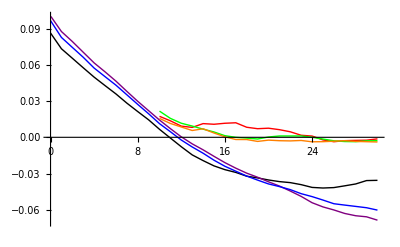

```mathematica
Fw[loci_]:=Transpose[{Range[0,30],Mean[((F[pp0⟦1;;45,#⟧,(*pp0⟦All,#⟧,*)30]+F[pp0⟦-45;;-1,#⟧,(*pp0⟦All,#⟧,*)30])/2)&/@loci]}];
Fb[loci_]:=DeleteCases[Transpose[{Range[0,30],Mean[(F[pp0⟦1;;45,#⟧,pp0⟦-45;;-1,#⟧,(*pp0⟦All,#⟧,*)10,30])&/@loci]}],{_,Indeterminate}];
l0=Join[Range[40,49],Range[51,60],Range[140,149],Range[151,160]];
lI=Join[Range[21,39],Range[61,80],Range[121,139],Range[161,180]];
lF=Join[Range[1,20],Range[81,120],Range[181,200]];
Show[MapThread[{ListLinePlot[Fw[#1],PlotRange->{{0,30},{-0.07,0.1}},PlotStyle->#2],ListLinePlot[Fb[#1],PlotStyle->#3]}&,{{l0,lI,lF},{Black,Purple, Blue},{Red,Green,Orange}}]]
```

```mathematica
ppF=alleleFreq[clF⟦-1⟧];ppFinit=alleleFreq[pF];
```

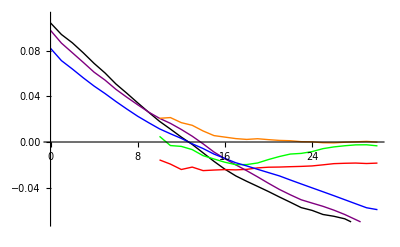

```mathematica
Fw[loci_]:=Transpose[{Range[0,30],Mean[((F[ppF⟦1;;45,#⟧,(*pp0⟦All,#⟧,*)30]+F[ppF⟦-45;;-1,#⟧,(*pp0⟦All,#⟧,*)30])/2)&/@loci]}];
Fb[loci_]:=DeleteCases[Transpose[{Range[0,30],Mean[(F[ppF⟦1;;45,#⟧,ppF⟦-45;;-1,#⟧,(*pp0⟦All,#⟧,*)10,30])&/@loci]}],{_,Indeterminate}];
l0=Join[Range[40,49],Range[51,60],Range[140,149],Range[151,160]];
lI=Join[Range[21,39],Range[61,80],Range[121,139],Range[161,180]];
lF=Join[Range[1,20],Range[81,120],Range[181,200]];
Show[MapThread[{ListLinePlot[Fw[#1],PlotRange->{{0,30},{-0.07,0.11}},PlotStyle->#2],ListLinePlot[Fb[#1],PlotStyle->#3]}&,{{l0,lI,lF},{Black,Purple, Blue},{Red,Green,Orange}}]]
```

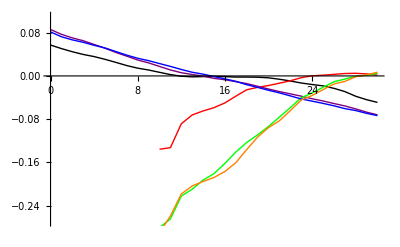

```mathematica
Fw[loci_]:=Transpose[{Range[0,30],Mean[((F[pp1⟦1;;45,#⟧,(*pp0⟦All,#⟧,*)30]+F[pp1⟦-45;;-1,#⟧,(*pp0⟦All,#⟧,*)30])/2)&/@loci]}];
Fb[loci_]:=DeleteCases[Transpose[{Range[0,30],Mean[(F[pp1⟦1;;45,#⟧,pp1⟦-45;;-1,#⟧,(*pp0⟦All,#⟧,*)10,30])&/@loci]}],{_,Indeterminate}];
l0=Join[Range[40,49],Range[51,60],Range[140,149],Range[151,160]];
lI=Join[Range[21,39],Range[61,80],Range[121,139],Range[161,180]];
lF=Join[Range[1,20],Range[81,120],Range[181,200]];
Show[MapThread[{ListLinePlot[Fw[#1],PlotRange->{{0,30},{-0.27,0.11}},PlotStyle->#2],ListLinePlot[Fb[#1],PlotStyle->#3]}&,{{l0,lI,lF},{Black,Purple, Blue},{Red,Green,Orange}}]]
```

### From “Joint distribution…”

#### expTw, expTb, Fst

```mathematica
expTw::usage="expTw[T,M,θ] gives the expected coalescence time for two genes sampled from within one of two demes. Split time, T, and migration rate, M, are scaled to 2N in the current population. θ is the ratio of ancestral to current population size. expTw[T,M,∞] gives the limit of Tw/θ as θ→∞, which equals the probability of coalescence before time T.";
```

```mathematica
expTw[T_,M_,θ_]:=Module[{γ=√(1+16 M^2)},
2+ⅇ^(-1/2 T (1+4 M)) (1/γ(4 M  (θ-2)-θ)Sinh[γ/2 T]+  (θ-2)Cosh[γ/2 T])];
expTw[T_,M_,∞]:=Module[{γ=√(1+16 M^2)},
ⅇ^(-1/2 (1+4 M) T) ( Cosh[γ/2  T]+((4 M-1)/γ) Sinh[γ/2  T])];
expTw[T_,0,θ_]:=1+ⅇ^-T (θ-1);
expTw[T_,0,∞]:=ⅇ^-T;
```

```mathematica
etw=-D[gfW[Λ,M,θ,ω],ω]/.ω->0//Simplify;
etb=-D[gfB[Λ,M,θ,ω],ω]/.ω->0//Simplify;Simplify/@Collect[(InverseLaplaceTransform[etw/Λ,Λ,T]/.{√(1+16 M^2)->γ,(1+16 M^2)^(-1/2)->1/γ}//Simplify)/.{ⅇ^(-1/2 T (1+4 M+γ))->z(c-s),ⅇ^(1/2 T (1+4 M+γ))->1/(z(c-s)),ⅇ^(T γ)->(c+s)/(c-s)},z]
```

2+(z (4 M s (-2+θ)+c γ (-2+θ)-s θ))/γ

```mathematica
{InverseLaplaceTransform[etw/Λ/.{M->2.2,θ->3},Λ,0.2],expTw[0.2,2.2,3]}
```

{2.77966,2.77966}

```mathematica
Limit[expTw[T,M,θ],M->0]
```

ⅇ^-T (-1+ⅇ^T+θ)

```mathematica
{expTw[0.2,0,3],expTw[0.2,0.000001,3]}
```

{2.63746,2.63746}

```mathematica
expTb::usage="expTb[T,M,θ] gives the expected coalescence time for two genes sampled from  two  different demes. Split time, T, and migration rate, M, are scaled to 2N in the current population. θ is the ratio of ancestral to current population size. expTb[T,M,∞] gives the limit of Tb/θ as θ→∞, which equals the probability of coalescence before time T.";
```

```mathematica
expTb[T_,M_,θ_]:=Module[{γ=√(1+16 M^2)},
 2((1+4M)/(4M))-ⅇ^(-1/2 T (1+4 M)) ((1/(2M)-(θ-2))Cosh[γ/2 T] + (1/(2M γ)-1/γ(1+4M)(θ-2)) Sinh[γ/2 T])];
```

```mathematica
expTb[T_,M_,∞]:=Module[{γ=√(1+16 M^2)},
 ⅇ^(-1/2 (1+4 M) T) ( Cosh[γ/2 T]+((1+4 M)/γ) Sinh[γ/2 T])];
```

```mathematica
expTb[T_,0,θ_]:=θ+T;
expTb[T_,0,∞]:=1;
```

```mathematica
{InverseLaplaceTransform[etb/Λ/.{M->2.2,θ->3},Λ,0.2],expTb[0.2,2.2,3]}
```

{3.04678,3.04678}

```mathematica
{expTb[0.2,0,3],expTb[0.2,0.00001,3]}
```

{3.2,3.2}

```mathematica
Simplify/@Collect[(InverseLaplaceTransform[etb/Λ,Λ,T]/.{√(1+16 M^2)->γ,(1+16 M^2)^(-1/2)->1/γ}//Simplify)/.{ⅇ^(-1/2 T (1+4 M+γ))->z(c-s),ⅇ^(1/2 T (1+4 M+γ))->1/(z(c-s)),ⅇ^(T γ)->(c+s)/(c-s)},z]
```

2+1/(2 M)+(z (c γ (-1+2 M (-2+θ))+s (-1+2 M (-2+θ)+8 M^2 (-2+θ))))/(2 M γ)

```mathematica
Fst::usage="Fst[T,M,θ] gives Fst for two demes with symmetric migration. Split time, T, and migration rate, M, are scaled to 2N in the current population. θ is the ratio of ancestral to current population size.";
```

```mathematica
Fst[T_,M_,θ_]:=(expTb[T,M,θ]-expTw[T,M,θ])/(expTb[T,M,θ]+expTw[T,M,θ]);
```

#### Meff

```mathematica
Meff::usage="Meff[r,Δr,s] gives m_eff/m, assuming two loci with selection s, at {0,Δr}";
```

```mathematica
Meff[r_,Δr_,s_]:=If[
r<0,-r/(-r+s)(s+(Δr-r))/(2s+(Δr-r)),If[r>Δr,
(r-Δr)/((r-Δr)+s)(s+r)/(2s+r),
r/(r+s)(Δr-r)/((Δr-r)+s)]];
```

#### barrier2

```mathematica
barrier2::usage="barrier[r,m,Δr,sol] gives B/σ for a neutral locus at position r, wth selected loci at {0,Δr}. The solution for the genotype frequencies is in the table sol. r=0 or Δr gives ∞";
```

```mathematica
barrier2[r_,m_,Δr_,sol_]:=If[r<0,
barrier[m,{-r,Δr},sol,-1],If[r>Δr,
barrier[m,{Δr,r-Δr},sol,1],
barrier[m,{r,Δr-r},sol,0]]];
```

#### ProbCoal

```mathematica
ProbCoal::usage="ProbCoal[B/σ,2N,T_m/δt] stores the probability of coalescence before time T_m, in steps of δt=100, with 200 demes; m=0.5";
```

```mathematica
ProbCoal[B_,n_,Tm_]:=ProbCoal[B,n,Tm]=NestList[iterP[0.5,n,1/(1+√0.5 B),100,100],ConstantArray[0,{200,200}],Round[Tm/100]];
```

#### fstP

```mathematica
fstP::usage="fstP[P,{x,y}] calculates F_st between demes x, y, assuming a deep ancestral population.";
```

```mathematica
fstP[P_,{x_,y_}]:=((P⟦x,x⟧+P⟦y,y⟧)/2-P⟦x,y⟧)/(2-((P⟦x,x⟧+P⟦y,y⟧)/2+P⟦x,y⟧));
```